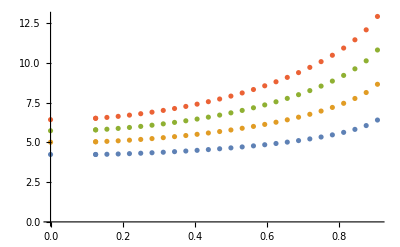

```mathematica
a={{0,4.244716},{0.125000,4.244530},{0.125000,4.244530},{0.156250,4.258162},{0.187500,4.276195},{0.218750,4.298251},{0.250000,4.324054},{0.281250,4.353424},{0.312500,4.386269},{0.343750,4.422572},{0.375000,4.462384},{0.406250,4.505824},{0.437500,4.553078},{0.468750,4.604402},{0.500000,4.660128},{0.531250,4.720674},{0.562500,4.786557},{0.593750,4.858417},{0.625000,4.937045},{0.656250,5.023435},{0.687500,5.118862},{0.718750,5.225009},{0.750000,5.344190},{0.781250,5.479776},{0.812500,5.637060},{0.843750,5.825373},{0.875000,6.064494},{0.906250,6.413725}};
a2={{0,5.017224},{0.125000,5.044317},{0.125000,5.044317},{0.156250,5.071560},{0.187500,5.105665},{0.218750,5.146164},{0.250000,5.192735},{0.281250,5.245203},{0.312500,5.303531},{0.343750,5.367792},{0.375000,5.438168},{0.406250,5.514937},{0.437500,5.598476},{0.468750,5.689257},{0.500000,5.787859},{0.531250,5.894970},{0.562500,6.011409},{0.593750,6.138151},{0.625000,6.276363},{0.656250,6.427475},{0.687500,6.593278},{0.718750,6.776105},{0.750000,6.979135},{0.781250,7.206970},{0.812500,7.466805},{0.843750,7.771185},{0.875000,8.146023},{0.906250,8.665163}};
a3={{0,5.738398},{0.125000,5.795001},{0.125000,5.795001},{0.156250,5.836123},{0.187500,5.886530},{0.218750,5.945660},{0.250000,6.013141},{0.281250,6.088805},{0.312500,6.172663},{0.343750,6.264875},{0.375000,6.365742},{0.406250,6.475690},{0.437500,6.595268},{0.468750,6.725148},{0.500000,6.866126},{0.531250,7.019135},{0.562500,7.185260},{0.593750,7.365768},{0.625000,7.562153},{0.656250,7.776215},{0.687500,8.010189},{0.718750,8.266963},{0.750000,8.550467},{0.781250,8.866395},{0.812500,9.223682},{0.843750,9.637920},{0.875000,10.141164},{0.906250,10.823716}};
a4={{0,6.436923},{0.125000,6.523608},{0.125000,6.523608},{0.156250,6.578583},{0.187500,6.645270},{0.218750,6.723001},{0.250000,6.811351},{0.281250,6.910157},{0.312500,7.019473},{0.343750,7.139547},{0.375000,7.270789},{0.406250,7.413767},{0.437500,7.569196},{0.468750,7.737933},{0.500000,7.920985},{0.531250,8.119510},{0.562500,8.334843},{0.593750,8.568520},{0.625000,8.822333},{0.656250,9.098421},{0.687500,9.399418},{0.718750,9.728718},{0.750000,10.090938},{0.781250,10.492790},{0.812500,10.944853},{0.843750,11.465665},{0.875000,12.093342},{0.906250,12.935130}};
ListPlot[{a,a2,a3,a4}]
```

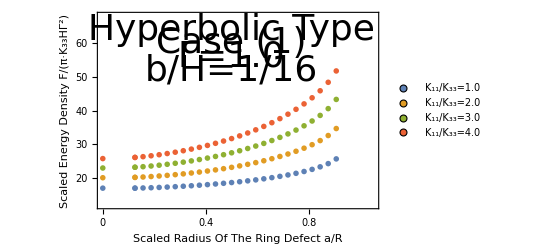

```mathematica
aa=a*Table[{1,4},{i,0,27}];
aa2=a2*Table[{1,4},{i,0,27}];
aa3=a3*Table[{1,4},{i,0,27}];
aa4=a4*Table[{1,4},{i,0,27}];
ListPlot[{aa,aa2,aa3,aa4},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{20,30,40,50,60},None},{{0,0.2, 0.4, 0.6, 0.8,1.0},None}}, PlotRange->{{0,1.05},{12,68}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=1.0","K_11/K_33=2.0","K_11/K_33=3.0","K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Hyperbolic Type",Directive[Black,36]],{0.5,64}],Text[Style["Case (1)",Directive[Black,36]],{0.5,60}],Text[Style["Γ=1.0",Directive[Black,36]],{0.5,56}],Text[Style["b/H=1/16",Directive[Black,36]],{0.5,52}]}]
```